```mathematica
Directory[]
```

C:\Users\USER\Documents

```mathematica
SetDirectory["D:\Dropbox\ExperimentDoc\[201206]SHARAQ04\DataAnalysis\Simulations\WSPOT\wspot"]
```

D:\Dropbox\ExperimentDoc\[201206]SHARAQ04\DataAnalysis\Simulations\WSPOT\wspot

```mathematica
Data=Import["fit.txt", "Data"];
```

```mathematica
data=DeleteCases[Data,Data[[220]]];
```

```mathematica
ListPlot3D[data]
```

-Graphics3D-

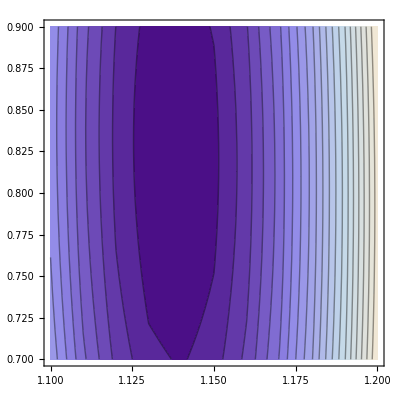

```mathematica
ListContourPlot[data,InterpolationOrder->3, Contours->20]
```